```mathematica
J2=0.2;
path="/Users/alexander/Documents/projects/NetKet/heisenberg/measurement/";
```

energy

```mathematica
data=Flatten[Import[path<>"/energy_J2="<>ToString[NumberForm[N[J2],{10,3}]]<>".txt","Table"],1];
```

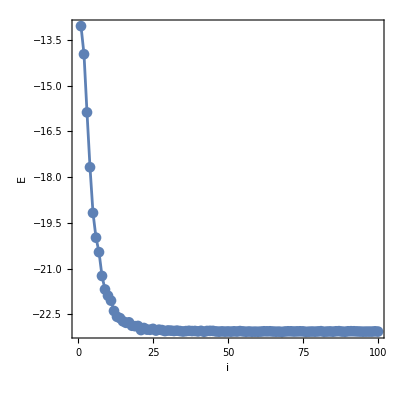

```mathematica
ListPlot[data[[1;;100]],Joined->True,PlotRange->All,PlotMarkers->Automatic,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"i","E"},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotStyle->ColorData[97,"ColorList"][[1]]]
```

```mathematica
data[[-1]]
```

-23.0676432277584027

structure factor

```mathematica
data=Flatten[Import[path<>"/sf_J2="<>ToString[NumberForm[N[J2],{10,3}]]<>".txt","Table"],1];
```

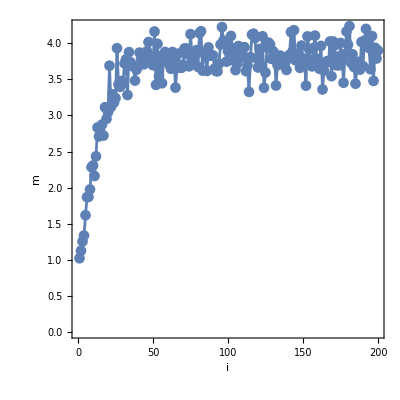

```mathematica
ListPlot[data[[1;;200]],Joined->True,PlotRange->All,PlotMarkers->Automatic,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"i","m"},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotStyle->ColorData[97,"ColorList"][[1]]]
```

```mathematica
J2=0.5;
path="/Users/alexander/Documents/projects/NetKet/heisenberg/measurement/";
```

```mathematica
data=Flatten[Import[path<>"/energy_J2="<>ToString[NumberForm[N[J2],{10,3}]]<>"_L=10_iter=300"<>".txt","Table"],1];
```

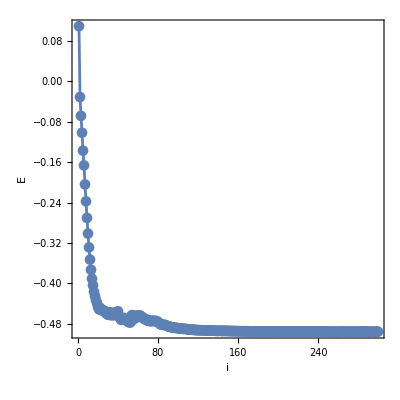

```mathematica
ListPlot[data[[1;;300]],Joined->True,PlotRange->All,PlotMarkers->Automatic,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"i","E"},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotStyle->ColorData[97,"ColorList"][[1]]]
```

```mathematica
5 16
```

80